```mathematica
Inverse[{{1+p/4(1/(2Jq)-(J^2-z^2)/(2Jqa)-1/a)(z+J),-(z-J)p/4(1/(2Jq)-(J^2-z^2)/(2Jqa)-1/a)},{(z+J)p/4(1/(2Jq)-(J^2-z^2)/(2Jqa)-1/a),1-(z-J)p/4(1/(2Jq)-(J^2-z^2)/(2Jqa)-1/a)}}]
```

{{(1-1/4 p (-J+z) (-1/a+1/(2 Jq)-(J^2-z^2)/(2 Jqa)))/(1-(J p)/(2 a)+(J p)/(4 Jq)-(J^3 p)/(4 Jqa)+(J p z^2)/(4 Jqa)),-(p (J-z) (-1/a+1/(2 Jq)-(J^2-z^2)/(2 Jqa)))/(4 (1-(J p)/(2 a)+(J p)/(4 Jq)-(J^3 p)/(4 Jqa)+(J p z^2)/(4 Jqa)))},{-(p (J+z) (-1/a+1/(2 Jq)-(J^2-z^2)/(2 Jqa)))/(4 (1-(J p)/(2 a)+(J p)/(4 Jq)-(J^3 p)/(4 Jqa)+(J p z^2)/(4 Jqa))),(1+1/4 p (J+z) (-1/a+1/(2 Jq)-(J^2-z^2)/(2 Jqa)))/(1-(J p)/(2 a)+(J p)/(4 Jq)-(J^3 p)/(4 Jqa)+(J p z^2)/(4 Jqa))}}

```mathematica
Inverse[{{1+p/4(1/(2Jq)-(J^2-z^2)/(2Jqa)+1/a)(z+J),-(z-J)p/4(1/(2Jq)-(J^2-z^2)/(2Jqa)+1/a)},{(z+J)p/4(1/(2Jq)-(J^2-z^2)/(2Jqa)+1/a),1-(z-J)p/4(1/(2Jq)-(J^2-z^2)/(2Jqa)+1/a)}}]
```

{{(1-1/4 p (-J+z) (1/a+1/(2 Jq)-(J^2-z^2)/(2 Jqa)))/(1+(J p)/(2 a)+(J p)/(4 Jq)-(J^3 p)/(4 Jqa)+(J p z^2)/(4 Jqa)),-(p (J-z) (1/a+1/(2 Jq)-(J^2-z^2)/(2 Jqa)))/(4 (1+(J p)/(2 a)+(J p)/(4 Jq)-(J^3 p)/(4 Jqa)+(J p z^2)/(4 Jqa)))},{-(p (J+z) (1/a+1/(2 Jq)-(J^2-z^2)/(2 Jqa)))/(4 (1+(J p)/(2 a)+(J p)/(4 Jq)-(J^3 p)/(4 Jqa)+(J p z^2)/(4 Jqa))),(1+1/4 p (J+z) (1/a+1/(2 Jq)-(J^2-z^2)/(2 Jqa)))/(1+(J p)/(2 a)+(J p)/(4 Jq)-(J^3 p)/(4 Jqa)+(J p z^2)/(4 Jqa))}}

```mathematica
(a-(J p)/2+(J p a)/(4 J q)-(J^3 p)/(4 J q)+(J p z^2)/(4 J q))/.{a->Sqrt[(J^2-z^2)^2-(2Jq)^2]}
```

-(J p)/2-(J^2 p)/(4 q)+(p z^2)/(4 q)+√(-4 Jq^2+(J^2-z^2)^2)+(p √(-4 Jq^2+(J^2-z^2)^2))/(4 q)

```mathematica
Solve[(J p)/2-(J^3 p)/(4 Jq)+(J p z^2)/(4 Jq)+√(-4 Jq^2+(J^2-z^2)^2)+(J p √(-4 Jq^2+(J^2-z^2)^2))/(4 Jq)==0,z]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{z→-√(J^2-2 Jq)},{z→√(J^2-2 Jq)},{z→-(√(-4 J^2 Jq-8 Jq^2-2 J^3 p-4 J Jq p-J^2 p^2))/(√(-4 Jq-2 J p))},{z→(√(-4 J^2 Jq-8 Jq^2-2 J^3 p-4 J Jq p-J^2 p^2))/(√(-4 Jq-2 J p))}}

```mathematica
Solve[-(J p)/2-(J^3 p)/(4 Jq)+(J p z^2)/(4 Jq)+√(-4 Jq^2+(J^2-z^2)^2)+(J p √(-4 Jq^2+(J^2-z^2)^2))/(4 Jq)==0,z]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{z→-√(J^2+2 Jq)},{z→√(J^2+2 Jq)},{z→-(√(-4 J^2 Jq+8 Jq^2-2 J^3 p+4 J Jq p+J^2 p^2))/(√(-4 Jq-2 J p))},{z→(√(-4 J^2 Jq+8 Jq^2-2 J^3 p+4 J Jq p+J^2 p^2))/(√(-4 Jq-2 J p))}}

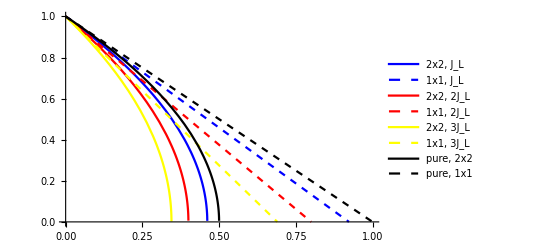

```mathematica
Plot[{(√(-6 q+13 q^2))/(√6 √-q),1-(q/2* (1+1/4)+q)/(1+1/2),(√(-8 q+20 q^2))/(2 √2 √-q),1-(5 q)/4,(√(-10 q+29 q^2))/(√10 √-q),1-(29 q)/20, Sqrt[1-2q], 1-q},{q,0,1},PlotStyle->{Blue,{Blue,Dashed},Red, {Red, Dashed},Yellow, {Yellow, Dashed}, Black, {Black, Dashed}},PlotRange->{0,1},PlotLegends->Placed[{"2x2, J_L","1x1, J_L","2x2, 2J_L","1x1, 2J_L","2x2, 3J_L","1x1, 3J_L", "pure, 2x2", "pure, 1x1"}, Above]]
```

```mathematica
(√(-4 *J^2 *J*q+8 J*q^2-2 J^3 p+4 J* J*q p+J^2 p^2))/(√(-4 J*q-2 J p))/.{J->1,p->3q}
```

(√(-10 q+29 q^2))/(√10 √-q)

```mathematica
1-(q+p/2(1+p/(4q)))/(1+p/(2q))/.{p->3q}
```

1-(29 q)/20